```mathematica
Clear["Global`*"];
Off[NIntegrate::slwcon];
Off[NIntegrate::ncvb];
```

```mathematica
(* If[n==0,0,(1-x)^1(1+x)^n x^0] || (1-x^2)×LegendreP[n,x] || LegendreP[n,x] *)
```

```mathematica
BasisFunction[n_]:=Function[{x},If[n==0,1,(1-x)^(n-1)(1+x)^1 x^0]];
BasisMin=0;
BasisMax=4;
Plot[Evaluate[Table[BasisFunction[n][x],{n,BasisMin,BasisMax}]],{x,-1,1},ImageSize->Medium,PlotRange->All];
```

```mathematica
PolinomeToCartesianBasis[y_]:=y.Table[BasisFunction[n][x],{n,BasisMin,BasisMax}];
```

```mathematica
qNonHomogeneous[x_]=PDF[NormalDistribution[0.1,0.2],x];
a=1;
b=-1;
qBoundary[x_]=-a+(b-a)/2(x+1);
qFunction[x_]=qNonHomogeneous[x];
q=Table[NIntegrate[qFunction[x]BasisFunction[n][x],{x,-1,1}],{n,BasisMin,BasisMax}];
Plot[{qFunction[x],PolinomeToCartesianBasis[q]+qBoundary[x]},{x,-1,1},PlotRange->All];
```

```mathematica
(L=Table[NIntegrate[(D[BasisFunction[m][x], x])×(D[BasisFunction[n][x], x]),{x,-1,1}],{n,BasisMin,BasisMax},{m,BasisMin,BasisMax}])//TableForm;
CoordinatesTable = Table[Subscript[c, i],{i,BasisMin,BasisMax}];
Functional = L[[3;;,3;;]].CoordinatesTable[[3;;]].CoordinatesTable[[3;;]]-2 q[[3;;]].CoordinatesTable[[3;;]];
```

```mathematica
Coordinates={a,(b-a)/2}~Join~(CoordinatesTable/.
NMinimize[Functional,CoordinatesTable[[3;;]]][[2]])[[3;;]];
```

```mathematica
AnaliticalSolution=y/.NDSolve[{D[y[x], x,x]==-qNonHomogeneous[x],y[-1]==a,y[+1]==b},y,{x,-1,1}][[1]];
```

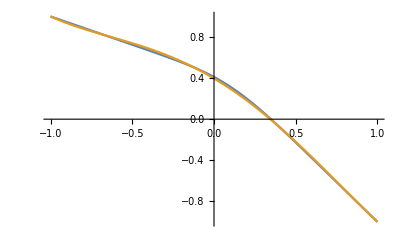

```mathematica
Plot[Evaluate[{AnaliticalSolution[x],PolinomeToCartesianBasis[Coordinates]}],{x,-1,1}]
```